```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210507_time_windows_and_OR_model"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package-2.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
stoichioforhomosapiens=Drop[Import["../210324_disc_time_windows_and_OR_model/iAT_PLT_636_stoichiomat.csv",HeaderLines->1],None,{1}];
SparseArray@stoichioforhomosapiens
```

SparseArray[…]

```mathematica
stoichiometricmatrix=stoichioforhomosapiens;
metabolites=738;
fluxexchanges=1008;
steadystatevector=ConstantArray[{0,0},metabolites];
first[a_]:=First/@GatherBy[Ordering@a,a[[#]]&]//Sort;
```

```mathematica
(* coefficients=Table[Table[RandomReal[{-1,1},Length@i],300],{i,subsetpositionsforsequences}]; *)
```

```mathematica
subsetpositionsforsequences=Import["subsetpositionsforsequences.mx"];
boundaries=Import["boundaries.mx"];
boundariespos=Flatten@Position[boundaries,{-5,5}];
coefficients=Import["coefficients.mx"];
```

```mathematica
boundariesa=ReplacePart[ConstantArray[{-500,500},fluxexchanges],MapThread[#1->#2&,{boundariespos,ConstantArray[{-0.5,0.5},Length@boundariespos]}]];
```

```mathematica
syntheticseqgenerator[stoichiometricmatrix_,steadystatevector_,boundaries_,fluxexchanges_,subsetpositions_,coefficients_]:=Module[{objectivefunctions,solutionvectors},
objectivefunctions=Table[ReplacePart[ConstantArray[0.,fluxexchanges],MapThread[#1->#2&,{subsetpositions,coefficients[[i]]}]],{i,300}];
solutionvectors=Chop[Table[LinearProgramming[-objectivefunctions[[i]],stoichiometricmatrix,steadystatevector,boundaries],{i,Length@objectivefunctions}],10^-5];{objectivefunctions,solutionvectors,MapThread[Dot,{objectivefunctions,solutionvectors}]}]
```

```mathematica
AbsoluteTiming[objfuncsforsequences=Table[syntheticseqgenerator[stoichiometricmatrix,steadystatevector,boundariesa,fluxexchanges,i[[1]],i[[2]]],{i,MapThread[{#1,#2}&,{subsetpositionsforsequences,coefficients}]}];]
```

LinearProgramming::lpipcv: Warning: the interior point algorithm cannot converge to the tolerance of 1.49012×10^-8. The best residual achieved is 5.77336×10^-8, and the solution at that residual has been returned. Setting the option Method -> RevisedSimplex should give a more definite answer, though large problems may take longer computing time.

LinearProgramming::lpipcv: Warning: the interior point algorithm cannot converge to the tolerance of 1.49012×10^-8. The best residual achieved is 6.60524×10^-8, and the solution at that residual has been returned. Setting the option Method -> RevisedSimplex should give a more definite answer, though large problems may take longer computing time.

LinearProgramming::lpipcv: Warning: the interior point algorithm cannot converge to the tolerance of 1.49012×10^-8. The best residual achieved is 2.36964×10^-8, and the solution at that residual has been returned. Setting the option Method -> RevisedSimplex should give a more definite answer, though large problems may take longer computing time.

General::stop: Further output of LinearProgramming::lpipcv will be suppressed during this calculation.

{5743.59,Null}

```mathematica
Length@first[(Flatten[objfuncsforsequences[[All,2]],1])ᵀ]
Length@(Flatten[objfuncsforsequences[[All,2]],1])[[first@Flatten[objfuncsforsequences[[All,2]],1],All]]
```

1008

60000

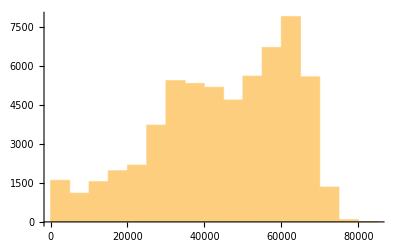

```mathematica
datafull=Join[Partition[Range@60000,1],Partition[Flatten@Table[ConstantArray[i,300],{i,200}],1],Partition[Flatten[objfuncsforsequences[[All,3]],1],1],2];
Histogram@datafull[[All,3]]
```

```mathematica
x2=Round@Ceiling[Length@datafull/19,1];
{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,r,s,t}=Join[Range[x2,Length@datafull,x2],{Length@datafull}];
data2=Join[{Take[datafull,{1,a}]},Flatten[Table[{Take[datafull,{z[[1]]-x2/2,z[[2]]-x2/2}],Take[datafull,{z[[1]],z[[2]]}]},{z,
Partition[{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,r,s,t},2,1]}],1]];
win2=Length@data2;
```

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep2=snetworkdatabinnedintimewindows[data2,3,1000,win2];]
```

{37.7859,Null}

```mathematica
graphsandnodenumbers12=Table[snetworkgraph[widthdataintimewindowsFixedstep2[[1]][[i]],widthdataintimewindowsFixedstep2[[2]][[i]],2,7,400,Green],{i,Range@win2}];
graphsandnodenumbers12[[All,2]]
```

{57,53,52,55,64,63,61,63,66,55,55,64,60,59,65,54,70,58,66,52,52,52,45,44,50,52,63,62,63,50,65,61,49,52,40,63,65}

```mathematica
modularityvalues12=Table[N@GraphAssortativity[graphsandnodenumbers12[[i]][[1]],FindGraphCommunities[graphsandnodenumbers12[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers12}];
```

```mathematica
singlerandomgraphsdegfxd12=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers12[[All,1]]}];
singlerandomerdrenmodularityvalues12=Table[N@GraphAssortativity[singlerandomgraphsdegfxd12[[i]],FindGraphCommunities[singlerandomgraphsdegfxd12[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd12}];
singlerandomgraphscomm12=Table[randomizinggraphmod[i],{i,graphsandnodenumbers12[[All,1]]}];
singlerandomcommmodularityvalues12=Table[N@GraphAssortativity[singlerandomgraphscomm12[[i]],FindGraphCommunities[singlerandomgraphscomm12[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm12}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity12=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers12[[All,1]]}];]
```

{1321.69,Null}

```mathematica
bucketnode12=graphsandnodenumbers12[[All,2]]
```

{57,53,52,55,64,63,61,63,66,55,55,64,60,59,65,54,70,58,66,52,52,52,45,44,50,52,63,62,63,50,65,61,49,52,40,63,65}

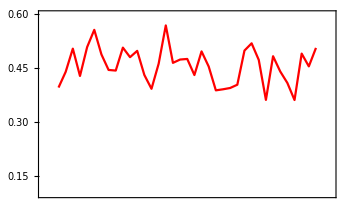
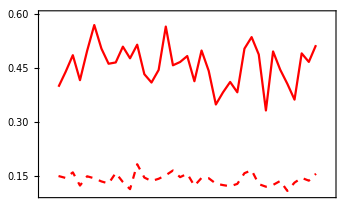
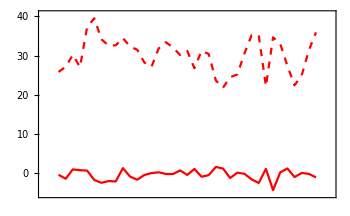

```mathematica
modularityvaluestimewinsmall=modularityvalues12;
randommodtimewinsmalldegreefxd=singlerandomerdrenmodularityvalues12;
randommodtimewinsmallcomm=singlerandomcommmodularityvalues12;
Zscoretimewinsmall=Zscoresmodularity12;
modularityplotrange={0.1,0.6};
(*MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,singlerandomerdrenmodularityvalues1,modularityvalues12}]*)
padding=38;
Row[{ListLinePlot[Thread[{Range@win2,modularityvaluestimewinsmall}],Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}],
Row[{ListLinePlot[{Thread[{Range@win2,randommodtimewinsmalldegreefxd}],Thread[{Range@win2,randommodtimewinsmallcomm}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}],
ListLinePlot[{Thread[{Range@win2,Zscoretimewinsmall[[All,1]]}],Thread[{Range@win2,Zscoretimewinsmall[[All,2]]}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{-1,win2+2},MinMax[Flatten[Zscoretimewinsmall],1]}]}],LineLegend[{Dashed,Black},{"Degrees Fixed N.M.","Modularity N.M."},LegendMargins->0,LegendMarkerSize->{20,20}],Spacer@0.1}]
```

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket2=snetworkdatafxdbucketintimewindows[data2,3,bucketnode12,win2];]
```

{5.59615,Null}

```mathematica
bucketsize32=Flatten@widthdataintimewindowsFixedbucket2[[4]]
```

{56,60,61,58,50,51,52,51,48,58,58,50,53,54,49,59,46,55,48,61,61,61,71,72,64,61,51,51,51,64,49,52,65,61,79,51,49}

```mathematica
graphsandnodenumbers32=Table[snetworkgraph[widthdataintimewindowsFixedbucket2[[1]][[i]],widthdataintimewindowsFixedbucket2[[2]][[i]],1.5,7,400,Green],{i,Range@win2}];
modularityvalues32=Table[N@GraphAssortativity[graphsandnodenumbers32[[i]][[1]],FindGraphCommunities[graphsandnodenumbers32[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers32}];
```

```mathematica
singlerandomgraphsdegfxd32=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers32[[All,1]]}];
singlerandomerdrenmodularityvalues32=Table[N@GraphAssortativity[singlerandomgraphsdegfxd32[[i]],FindGraphCommunities[singlerandomgraphsdegfxd32[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd32}];
singlerandomgraphscomm32=Table[randomizinggraphmod[i],{i,graphsandnodenumbers32[[All,1]]}];
singlerandomcommmodularityvalues32=Table[N@GraphAssortativity[singlerandomgraphscomm32[[i]],FindGraphCommunities[singlerandomgraphscomm32[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm32}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity32=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers32[[All,1]]}];]
```

{1149.51,Null}

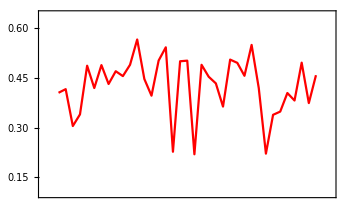
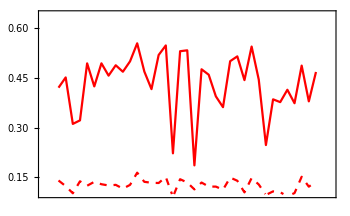
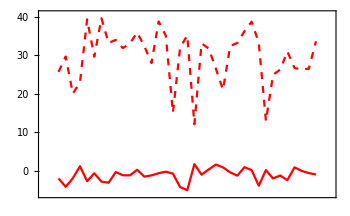

```mathematica
modularityvaluestimewinsmall=modularityvalues32;
randommodtimewinsmalldegreefxd=singlerandomerdrenmodularityvalues32;
randommodtimewinsmallcomm=singlerandomcommmodularityvalues32;
Zscoretimewinsmall=Zscoresmodularity32;
modularityplotrange={0.1,0.64};
(*MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,singlerandomerdrenmodularityvalues1,modularityvalues12}]*)
padding=38;
Row[{ListLinePlot[Thread[{Range@win2,modularityvaluestimewinsmall}],Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}],
Row[{ListLinePlot[{Thread[{Range@win2,randommodtimewinsmalldegreefxd}],Thread[{Range@win2,randommodtimewinsmallcomm}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}],
ListLinePlot[{Thread[{Range@win2,Zscoretimewinsmall[[All,1]]}],Thread[{Range@win2,Zscoretimewinsmall[[All,2]]}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{-1,win2+2},MinMax[Flatten[Zscoretimewinsmall],1]}]}],LineLegend[{Dashed,Black},{"Degrees Fixed N.M.","Modularity N.M."},LegendMargins->0,LegendMarkerSize->{20,20}],Spacer@0.1}]
```

```mathematica
Export["plot_values/boundaries_(-0.5,0.5)-modularityvalues-fss.mx",modularityvalues12]
Export["plot_values/boundaries_(-0.5,0.5)-singrand-erd-modularityvalues-fss.mx",singlerandomerdrenmodularityvalues12]
Export["plot_values/boundaries_(-0.5,0.5)-singrand-comm-modularityvalues-fss.mx",singlerandomcommmodularityvalues12]
Export["plot_values/boundaries_(-0.5,0.5)-zscores-fss.mx",Zscoresmodularity12]
Export["plot_values/boundaries_(-0.5,0.5)-modularityvalues-fbs.mx",modularityvalues32]
Export["plot_values/boundaries_(-0.5,0.5)-singrand-erd-modularityvalues-fbs.mx",singlerandomerdrenmodularityvalues32]
Export["plot_values/boundaries_(-0.5,0.5)-singrand-comm-modularityvalues-fbs.mx",singlerandomcommmodularityvalues32]
Export["plot_values/boundaries_(-0.5,0.5)-zscores-fbs.mx",Zscoresmodularity32]
```

plot_values/boundaries_(-0.5,0.5)-modularityvalues-fss.mx

plot_values/boundaries_(-0.5,0.5)-singrand-erd-modularityvalues-fss.mx

plot_values/boundaries_(-0.5,0.5)-singrand-comm-modularityvalues-fss.mx

plot_values/boundaries_(-0.5,0.5)-zscores-fss.mx

plot_values/boundaries_(-0.5,0.5)-modularityvalues-fbs.mx

plot_values/boundaries_(-0.5,0.5)-singrand-erd-modularityvalues-fbs.mx

plot_values/boundaries_(-0.5,0.5)-singrand-comm-modularityvalues-fbs.mx

plot_values/boundaries_(-0.5,0.5)-zscores-fbs.mx